```mathematica
d=Monitor[Table[
With[{g=JacobsThalGraph[k]},
With[
{h=Rule2[g,1<->4,5<->2]},
x/.NSolve[ChromaticPolynomial[g,x]==0,x]
]
]
,{k,1,20}],k]
```

{{0.+0. ⅈ,1.,2.,3.,3.},{0.+0. ⅈ,1.,2.,2.5466,3.2267-1.46771 ⅈ,3.2267+1.46771 ⅈ},{0.+0. ⅈ,1.,2.,2.67781,3.,3.16109-1.75438 ⅈ,3.16109+1.75438 ⅈ},{0.+0. ⅈ,1.,2.,2.59483,2.76469-0.754442 ⅈ,2.76469+0.754442 ⅈ,3.43789-1.93908 ⅈ,3.43789+1.93908 ⅈ},{0.+0. ⅈ,1.,2.,2.5-0.866025 ⅈ,2.5+0.866025 ⅈ,2.63612,3.,3.68194-2.24304 ⅈ,3.68194+2.24304 ⅈ},{0.+0. ⅈ,1.,2.,2.38733-0.85479 ⅈ,2.38733+0.85479 ⅈ,2.60913,2.90313-0.564564 ⅈ,2.90313+0.564564 ⅈ,3.90498-2.49614 ⅈ,3.90498+2.49614 ⅈ},{0.+0. ⅈ,1.,2.,2.33924-0.773092 ⅈ,2.33924+0.773092 ⅈ,2.62436,2.71292-0.893125 ⅈ,2.71292+0.893125 ⅈ,3.,4.13566-2.73568 ⅈ,4.13566+2.73568 ⅈ},{0.+0. ⅈ,1.,2.,2.26779-0.686958 ⅈ,2.26779+0.686958 ⅈ,2.61454,2.61852-1.08536 ⅈ,2.61852+1.08536 ⅈ,2.94226-0.423335 ⅈ,2.94226+0.423335 ⅈ,4.36416-2.96498 ⅈ,4.36416+2.96498 ⅈ},{0.+0. ⅈ,1.,2.,2.21536-0.627822 ⅈ,2.21536+0.627822 ⅈ,2.58971-1.19132 ⅈ,2.58971+1.19132 ⅈ,2.62036,2.79356-0.689903 ⅈ,2.79356+0.689903 ⅈ,3.,4.59119-3.18453 ⅈ,4.59119+3.18453 ⅈ},{0.+0. ⅈ,1.,2.,2.17868-0.576815 ⅈ,2.17868+0.576815 ⅈ,2.61433-1.29511 ⅈ,2.61433+1.29511 ⅈ,2.61667,2.62045-0.828219 ⅈ,2.62045+0.828219 ⅈ,2.9615-0.337218 ⅈ,2.9615+0.337218 ⅈ,4.8167-3.39603 ⅈ,4.8167+3.39603 ⅈ},{0.+0. ⅈ,1.,2.,2.15045-0.532109 ⅈ,2.15045+0.532109 ⅈ,2.5-0.866025 ⅈ,2.5+0.866025 ⅈ,2.61891,2.63877-1.4238 ⅈ,2.63877+1.4238 ⅈ,2.86071-0.577822 ⅈ,2.86071+0.577822 ⅈ,3.,5.04062-3.60058 ⅈ,5.04062+3.60058 ⅈ},{0.+0. ⅈ,1.,2.,2.12817-0.493323 ⅈ,2.12817+0.493323 ⅈ,2.4392-0.862481 ⅈ,2.4392+0.862481 ⅈ,2.61751,2.65614-1.54855 ⅈ,2.65614+1.54855 ⅈ,2.73249-0.750596 ⅈ,2.73249+0.750596 ⅈ,2.97228-0.279336 ⅈ,2.97228+0.279336 ⅈ,5.26298-3.79904 ⅈ,5.26298+3.79904 ⅈ},{0.+0. ⅈ,1.,2.,2.11039-0.459475 ⅈ,2.11039+0.459475 ⅈ,2.4062-0.819419 ⅈ,2.4062+0.819419 ⅈ,2.6155-0.891771 ⅈ,2.6155+0.891771 ⅈ,2.61837,2.67607-1.67058 ⅈ,2.67607+1.67058 ⅈ,2.89885-0.493389 ⅈ,2.89885+0.493389 ⅈ,3.,5.4838-3.99212 ⅈ,5.4838+3.99212 ⅈ},{0.+0. ⅈ,1.,2.,2.09601-0.429722 ⅈ,2.09601+0.429722 ⅈ,2.35478-0.768849 ⅈ,2.35478+0.768849 ⅈ,2.56121-0.99369 ⅈ,2.56121+0.99369 ⅈ,2.61782,2.69761-1.7925 ⅈ,2.69761+1.7925 ⅈ,2.7993-0.65546 ⅈ,2.7993+0.65546 ⅈ,2.97908-0.238054 ⅈ,2.97908+0.238054 ⅈ,5.70315-4.1804 ⅈ,5.70315+4.1804 ⅈ},{0.+0. ⅈ,1.,2.,2.08422-0.403406 ⅈ,2.08422+0.403406 ⅈ,2.3116-0.732179 ⅈ,2.3116+0.732179 ⅈ,2.54284-1.05616 ⅈ,2.54284+1.05616 ⅈ,2.62045,2.68764-0.774243 ⅈ,2.68764+0.774243 ⅈ,2.72005-1.91399 ⅈ,2.72005+1.91399 ⅈ,2.92309-0.429531 ⅈ,2.92309+0.429531 ⅈ,2.99999,5.92108-4.36435 ⅈ,5.92108+4.36435 ⅈ},{0.+0. ⅈ,1.,2.,2.07444-0.379986 ⅈ,2.07464+0.379929 ⅈ,2.27774+0.697979 ⅈ,2.27792-0.698094 ⅈ,2.5514-1.1173 ⅈ,2.5514+1.1173 ⅈ,2.57781-0.843704 ⅈ,2.57789+0.843747 ⅈ,2.61504,2.74345-2.03494 ⅈ,2.74345+2.03494 ⅈ,2.84347+0.581549 ⅈ,2.84494-0.582133 ⅈ,2.98356-0.207306 ⅈ,2.98366+0.207212 ⅈ,6.13766-4.54438 ⅈ,6.13766+4.54438 ⅈ},{0.+0. ⅈ,1.,2.00005,2.06624+0.358974 ⅈ,2.06698-0.360089 ⅈ,2.24747+0.666201 ⅈ,2.2487-0.667491 ⅈ,2.49968-0.865942 ⅈ,2.49986+0.866055 ⅈ,2.56065+1.19191 ⅈ,2.56065-1.19192 ⅈ,2.6309,2.75533-0.702651 ⅈ,2.75673+0.705735 ⅈ,2.76777-2.15541 ⅈ,2.76777+2.15541 ⅈ,2.92924,2.93781,2.99938,6.35293+4.72084 ⅈ,6.35293-4.72084 ⅈ},{0.+0. ⅈ,1.,1.99965,2.05825+0.33815 ⅈ,2.0593-0.340546 ⅈ,2.21545-0.632397 ⅈ,2.22887,2.46034,2.46227,2.56504-1.26512 ⅈ,2.56506+1.26515 ⅈ,2.56882,2.62727,2.65152,2.79294+2.27543 ⅈ,2.79294-2.27543 ⅈ,2.86998,2.89417,2.97896,3.02852,6.56696+4.89401 ⅈ,6.56696-4.89401 ⅈ},{0.+0. ⅈ,1.,1.98888,2.05829,2.07945,2.18716,2.26084,2.2798,2.31366,2.46607,2.48882,2.57022+1.33655 ⅈ,2.57042-1.33628 ⅈ,2.64066,2.81697,2.81891+2.39501 ⅈ,2.81891-2.39501 ⅈ,2.86773,2.92433,3.07963,3.14279,6.77979+5.06415 ⅈ,6.77979-5.06415 ⅈ},{0.+0. ⅈ,1.,2.01987,2.03853,2.04142,2.0492,2.16638,2.16892,2.28126,2.28171,2.50079,2.51282,2.57593+1.40819 ⅈ,2.57612-1.40788 ⅈ,2.72687,2.84561-2.51417 ⅈ,2.84561+2.51417 ⅈ,2.88163,3.03368,3.04039,3.19285,3.20009,6.99149-5.23149 ⅈ,6.99149+5.23149 ⅈ}}

```mathematica
d2=Monitor[Table[
With[{g=JacobsThalGraph[k]},
With[
{h=Rule2[g,1<->4,5<->2]},
x/.NSolve[ChromaticPolynomial[h,x]==0,x]
]
]
,{k,1,20}],k]
```

{{0.+0. ⅈ,1.,2.,3.,3.,3.},{0.+0. ⅈ,1.,2.,2.67781,3.,3.16109-1.75438 ⅈ,3.16109+1.75438 ⅈ},{0.+0. ⅈ,1.,2.,2.61497,2.88928-2.06647 ⅈ,2.88928+2.06647 ⅈ,3.,3.60646},{0.+0. ⅈ,1.,2.,2.63005,2.97351-2.137 ⅈ,2.97351+2.137 ⅈ,3.,3.21147-0.739653 ⅈ,3.21147+0.739653 ⅈ},{0.+0. ⅈ,1.,2.,2.61475,2.71933-0.952969 ⅈ,2.71933+0.952969 ⅈ,3.,3.23284-2.32695 ⅈ,3.23284+2.32695 ⅈ,3.48092},{0.+0. ⅈ,1.,2.,2.49784-0.938375 ⅈ,2.49784+0.938375 ⅈ,2.62159,3.,3.2462-0.540801 ⅈ,3.2462+0.540801 ⅈ,3.44517-2.53171 ⅈ,3.44517+2.53171 ⅈ},{0.+0. ⅈ,1.,2.,2.41411-0.858317 ⅈ,2.41411+0.858317 ⅈ,2.61645,2.91209-0.911432 ⅈ,2.91209+0.911432 ⅈ,3.,3.36654,3.6823-2.71843 ⅈ,3.6823+2.71843 ⅈ},{0.+0. ⅈ,1.,2.,2.33222-0.743913 ⅈ,2.33222+0.743913 ⅈ,2.61925,2.71254-1.14917 ⅈ,2.71254+1.14917 ⅈ,3.,3.2179-0.391132 ⅈ,3.2179+0.391132 ⅈ,3.92771-2.91242 ⅈ,3.92771+2.91242 ⅈ},{0.+0. ⅈ,1.,2.,2.26001-0.66902 ⅈ,2.26001+0.66902 ⅈ,2.61738,2.626-1.27214 ⅈ,2.626+1.27214 ⅈ,2.98475-0.67635 ⅈ,2.98475+0.67635 ⅈ,3.,3.29584,4.17264-3.10747 ⅈ,4.17264+3.10747 ⅈ},{0.+0. ⅈ,1.,2.,2.21115-0.610133 ⅈ,2.21115+0.610133 ⅈ,2.60571-1.36884 ⅈ,2.60571+1.36884 ⅈ,2.61848,2.76117-0.841702 ⅈ,2.76117+0.841702 ⅈ,3.,3.19722-0.304228 ⅈ,3.19722+0.304228 ⅈ,4.41551-3.30199 ⅈ,4.41551+3.30199 ⅈ},{0.+0. ⅈ,1.,2.,2.17528-0.559619 ⅈ,2.17528+0.559619 ⅈ,2.59477-0.898051 ⅈ,2.59477+0.898051 ⅈ,2.60728-1.48463 ⅈ,2.60728+1.48463 ⅈ,2.61779,3.,3.03365-0.554086 ⅈ,3.03365+0.554086 ⅈ,3.24969,4.65528-3.49473 ⅈ,4.65528+3.49473 ⅈ},{0.+0. ⅈ,1.,2.,2.14757-0.516305 ⅈ,2.14757+0.516305 ⅈ,2.50199-0.900367 ⅈ,2.50199+0.900367 ⅈ,2.60478-1.60102 ⅈ,2.60478+1.60102 ⅈ,2.6182,2.86599-0.742944 ⅈ,2.86599+0.742944 ⅈ,3.,3.17877-0.248423 ⅈ,3.17877+0.248423 ⅈ,4.89179-3.68488 ⅈ,4.89179+3.68488 ⅈ},{0.+0. ⅈ,1.,2.,2.12581-0.478974 ⅈ,2.12581+0.478974 ⅈ,2.45613-0.865894 ⅈ,2.45613+0.865894 ⅈ,2.60714-1.71163 ⅈ,2.60714+1.71163 ⅈ,2.61768,2.7129-0.891013 ⅈ,2.7129+0.891013 ⅈ,2.99992,3.05532-0.465894 ⅈ,3.05532+0.465894 ⅈ,3.21761,5.12518-3.87207 ⅈ,5.12518+3.87207 ⅈ},{0.+0. ⅈ,1.,2.,2.10846+0.446481 ⅈ,2.10846-0.446479 ⅈ,2.40269+0.80533 ⅈ,2.40271-0.805323 ⅈ,2.61568+1.82078 ⅈ,2.61568-1.82078 ⅈ,2.61924,2.62254+1.01291 ⅈ,2.62254-1.01292 ⅈ,2.92273-0.641185 ⅈ,2.92275+0.64119 ⅈ,2.99899,3.16244-0.212226 ⅈ,3.16315+0.209603 ⅈ,5.35568-4.05615 ⅈ,5.35568+4.05615 ⅈ},{0.+0. ⅈ,1.,2.00001,2.09441-0.417967 ⅈ,2.09443+0.417971 ⅈ,2.34953-0.761177 ⅈ,2.34965+0.761637 ⅈ,2.58297+1.08732 ⅈ,2.58297-1.08733 ⅈ,2.61197,2.62868-1.92974 ⅈ,2.62868+1.92974 ⅈ,2.78885-0.771322 ⅈ,2.78915+0.771378 ⅈ,2.98629,3.06379+0.410304 ⅈ,3.06932,3.16399,5.58353+4.23711 ⅈ,5.58353-4.23711 ⅈ},{0.+0. ⅈ,1.,2.00005,2.0827+0.392799 ⅈ,2.08285-0.392869 ⅈ,2.30769-0.72313 ⅈ,2.30872+0.724067 ⅈ,2.56996,2.57467+1.14931 ⅈ,2.57482-1.14955 ⅈ,2.64538+2.03876 ⅈ,2.64538-2.03876 ⅈ,2.66062+0.854217 ⅈ,2.66455-0.853739 ⅈ,2.94909,2.95002,3.12381,3.14236,3.20157,5.80897+4.41504 ⅈ,5.80897-4.41504 ⅈ},{0.+0. ⅈ,1.,2.0002,2.0734-0.370233 ⅈ,2.07345+0.370066 ⅈ,2.27513-0.689067 ⅈ,2.27517+0.688555 ⅈ,2.49537,2.56059-0.884915 ⅈ,2.56072+0.885687 ⅈ,2.57563+1.22342 ⅈ,2.57567-1.2234 ⅈ,2.6652+2.14813 ⅈ,2.6652-2.14813 ⅈ,2.82994,2.84352,2.95659,3.0446,3.17098,3.18708,6.03222-4.59003 ⅈ,6.03222+4.59003 ⅈ},{0.+0. ⅈ,1.,1.99902,2.06531,2.06617,2.25904,2.25989,2.26537,2.52016,2.53502,2.56431,2.57102-1.29834 ⅈ,2.57104+1.29753 ⅈ,2.68758-2.25805 ⅈ,2.68758+2.25805 ⅈ,2.75585,2.92301,3.07382,3.11147,3.30575,3.32183,6.25344+4.76223 ⅈ,6.25344-4.76223 ⅈ},{0.+0. ⅈ,1.,2.03734,2.03796,2.05143,2.0848,2.20255,2.21145,2.33615,2.41343,2.54634,2.56661-1.36968 ⅈ,2.56748+1.36896 ⅈ,2.5806,2.71206-2.36857 ⅈ,2.71206+2.36857 ⅈ,2.85915,2.99539,3.13225,3.20635,3.35389,3.36749,6.47281+4.93176 ⅈ,6.47281-4.93176 ⅈ},{0.+0. ⅈ,1.,1.98726,1.99095,2.01195,2.02383,2.1344,2.14145,2.21264,2.33077,2.44332,2.54417,2.56375-1.43925 ⅈ,2.5648+1.43822 ⅈ,2.6851,2.73824-2.47967 ⅈ,2.73824+2.47967 ⅈ,2.9396,3.09098,3.39281,3.44351,3.44503,3.48746,6.69045-5.09877 ⅈ,6.69045+5.09877 ⅈ}}

```mathematica
d3=Monitor[Table[
With[{g=JacobsThalGraph[k]},
With[
{h=Rule2[g,1<->4,5<->2]},
x/.NSolve[ChromaticPolynomial[g,x]/ChromaticPolynomial[h,x]==0,x]
]
]
,{k,1,20}],k]
```

{x,{3.2267+1.46771 ⅈ,3.2267-1.46771 ⅈ,2.5466},{3.16109+1.75438 ⅈ,3.16109-1.75438 ⅈ,2.67781},{3.43789+1.93908 ⅈ,3.43789-1.93908 ⅈ,2.76469+0.754442 ⅈ,2.76469-0.754442 ⅈ,2.59483},{3.68194+2.24304 ⅈ,3.68194-2.24304 ⅈ,2.5+0.866025 ⅈ,2.5-0.866025 ⅈ,2.63612},{3.90498+2.49614 ⅈ,3.90498-2.49614 ⅈ,2.90313+0.564564 ⅈ,2.90313-0.564564 ⅈ,2.60913,2.38733+0.85479 ⅈ,2.38733-0.85479 ⅈ},{4.13566+2.73568 ⅈ,4.13566-2.73568 ⅈ,2.71292+0.893125 ⅈ,2.71292-0.893125 ⅈ,2.62436,2.33924+0.773092 ⅈ,2.33924-0.773092 ⅈ},{4.36416+2.96498 ⅈ,4.36416-2.96498 ⅈ,2.94226+0.423335 ⅈ,2.94226-0.423335 ⅈ,2.61852+1.08536 ⅈ,2.61852-1.08536 ⅈ,2.61454,2.26779+0.686958 ⅈ,2.26779-0.686958 ⅈ},{4.59119+3.18453 ⅈ,4.59119-3.18453 ⅈ,2.79356+0.689903 ⅈ,2.79356-0.689903 ⅈ,2.58971+1.19132 ⅈ,2.58971-1.19132 ⅈ,2.62036,2.21536+0.627822 ⅈ,2.21536-0.627822 ⅈ},{4.8167+3.39603 ⅈ,4.8167-3.39603 ⅈ,2.9615+0.337218 ⅈ,2.9615-0.337218 ⅈ,2.61433+1.29511 ⅈ,2.61433-1.29511 ⅈ,2.62045+0.828219 ⅈ,2.62045-0.828219 ⅈ,2.61667,2.17868+0.576815 ⅈ,2.17868-0.576815 ⅈ},{5.04062+3.60058 ⅈ,5.04062-3.60058 ⅈ,2.63877+1.4238 ⅈ,2.63877-1.4238 ⅈ,2.86071+0.577822 ⅈ,2.86071-0.577822 ⅈ,2.5+0.866025 ⅈ,2.5-0.866025 ⅈ,2.61891,2.15045+0.532109 ⅈ,2.15045-0.532109 ⅈ},{5.26298+3.79904 ⅈ,5.26298-3.79904 ⅈ,2.65614+1.54855 ⅈ,2.65614-1.54855 ⅈ,2.97227+0.279336 ⅈ,2.97227-0.279336 ⅈ,2.73249+0.750596 ⅈ,2.73249-0.750596 ⅈ,2.4392+0.862481 ⅈ,2.4392-0.862481 ⅈ,2.12817+0.493323 ⅈ,2.12817-0.493323 ⅈ},{5.4838+3.99212 ⅈ,5.4838-3.99212 ⅈ,2.67607+1.67058 ⅈ,2.67607-1.67058 ⅈ,2.89885+0.49339 ⅈ,2.89885-0.49339 ⅈ,2.6155+0.891771 ⅈ,2.6155-0.891771 ⅈ,2.61836,2.4062+0.819419 ⅈ,2.4062-0.819419 ⅈ,2.11039+0.459475 ⅈ,2.11039-0.459475 ⅈ},{5.70315+4.1804 ⅈ,5.70315-4.1804 ⅈ,2.69761+1.7925 ⅈ,2.69761-1.7925 ⅈ,2.97903+0.238025 ⅈ,2.97903-0.238025 ⅈ,2.7993+0.655466 ⅈ,2.7993-0.655466 ⅈ,2.56121+0.99369 ⅈ,2.56121-0.99369 ⅈ,2.61782,2.35478+0.768849 ⅈ,2.35478-0.768849 ⅈ,2.09601+0.429722 ⅈ,2.09601-0.429722 ⅈ},{5.92108+4.36435 ⅈ,5.92108-4.36435 ⅈ,2.72005+1.91399 ⅈ,2.72005-1.91399 ⅈ,2.92311+0.429542 ⅈ,2.92311-0.429542 ⅈ,2.68799+0.774051 ⅈ,2.68799-0.774051 ⅈ,2.54284+1.05616 ⅈ,2.54284-1.05616 ⅈ,2.31162+0.732125 ⅈ,2.31162-0.732125 ⅈ,2.08422+0.403407 ⅈ,2.08422-0.403407 ⅈ},{6.13766+4.54438 ⅈ,6.13766-4.54438 ⅈ,2.74345+2.03494 ⅈ,2.74345-2.03494 ⅈ,2.55141+1.1173 ⅈ,2.55141-1.1173 ⅈ,2.57786+0.843768 ⅈ,2.57786-0.843768 ⅈ,2.27779+0.697942 ⅈ,2.27779-0.697942 ⅈ,2.07444+0.379994 ⅈ,2.07444-0.379994 ⅈ},{6.35293+4.72084 ⅈ,6.35293-4.72084 ⅈ,2.76777+2.15541 ⅈ,2.76777-2.15541 ⅈ,2.56066+1.19191 ⅈ,2.56066-1.19191 ⅈ},{6.56696+4.89401 ⅈ,6.56696-4.89401 ⅈ,2.79294+2.27543 ⅈ,2.79294-2.27543 ⅈ},{6.77979+5.06415 ⅈ,6.77979-5.06415 ⅈ,2.81891+2.39501 ⅈ,2.81891-2.39501 ⅈ,2.57018+1.3365 ⅈ,2.57018-1.3365 ⅈ},{6.99149+5.23149 ⅈ,6.99149-5.23149 ⅈ,2.84561+2.51417 ⅈ,2.84561-2.51417 ⅈ,2.57607+1.40787 ⅈ,2.57607-1.40787 ⅈ}}

```mathematica
Flatten[Out[36]]
```

{0.+0. ⅈ,1.,2.,3.,3.,4.,0.+0. ⅈ,1.,2.,2.59272,3.30589-1.73001 ⅈ,3.30589+1.73001 ⅈ,3.7955,0.+0. ⅈ,1.,2.,2.64294,3.,3.0396-2.09327 ⅈ,3.0396+2.09327 ⅈ,4.27785,0.+0. ⅈ,1.,2.,2.6085,2.93774-0.638315 ⅈ,2.93774+0.638315 ⅈ,3.1352-2.22871 ⅈ,3.1352+2.22871 ⅈ,4.24562,0.+0. ⅈ,1.,2.,2.62563,2.63123-0.880346 ⅈ,2.63123+0.880346 ⅈ,3.,3.34437-2.46218 ⅈ,3.34437+2.46218 ⅈ,4.42316,0.+0. ⅈ,1.,2.,2.46477-0.894124 ⅈ,2.46477+0.894124 ⅈ,2.61418,2.97285-0.467243 ⅈ,2.97285+0.467243 ⅈ,3.52516-2.68064 ⅈ,3.52516+2.68064 ⅈ,4.46027,0.+0. ⅈ,1.,2.,2.40042-0.819813 ⅈ,2.40042+0.819813 ⅈ,2.62072,2.80023-0.850679 ⅈ,2.80023+0.850679 ⅈ,3.,3.72771-2.87476 ⅈ,3.72771+2.87476 ⅈ,4.52256,0.+0. ⅈ,1.,2.,2.31534-0.715943 ⅈ,2.31534+0.715943 ⅈ,2.61651,2.67917-1.10172 ⅈ,2.67917+1.10172 ⅈ,2.97861-0.355185 ⅈ,2.97861+0.355185 ⅈ,3.943-3.06359 ⅈ,3.943+3.06359 ⅈ,4.55125,0.+0. ⅈ,1.,2.,2.24827-0.650409 ⅈ,2.24827+0.650409 ⅈ,2.61903,2.62328-1.23238 ⅈ,2.62328+1.23238 ⅈ,2.86572-0.638905 ⅈ,2.86572+0.638905 ⅈ,3.,4.1651-3.24766 ⅈ,4.1651+3.24766 ⅈ,4.57622,0.+0. ⅈ,1.,2.,2.20293-0.595853 ⅈ,2.20293+0.595853 ⅈ,2.61744,2.62033-1.33923 ⅈ,2.62033+1.33923 ⅈ,2.6981-0.811313 ⅈ,2.6981+0.811313 ⅈ,2.98286-0.288376 ⅈ,2.98286+0.288376 ⅈ,4.39172-3.42872 ⅈ,4.39172+3.42872 ⅈ,4.59068}

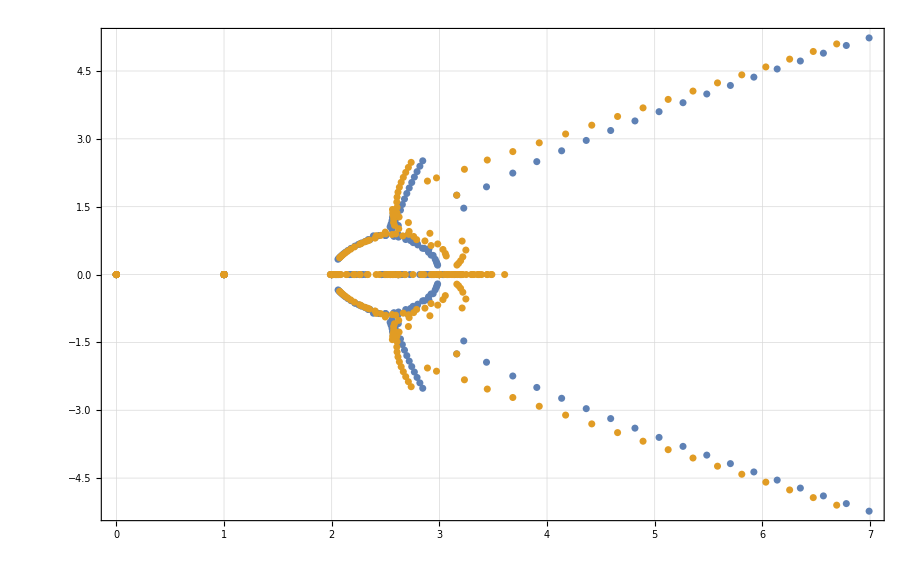

```mathematica
ListPlot[{Map[{Re[#],Im[#]}&,Flatten[d]],Map[{Re[#],Im[#]}&,Flatten[d2]]}, PlotRange->All,GridLines->Automatic,Frame->True]
```

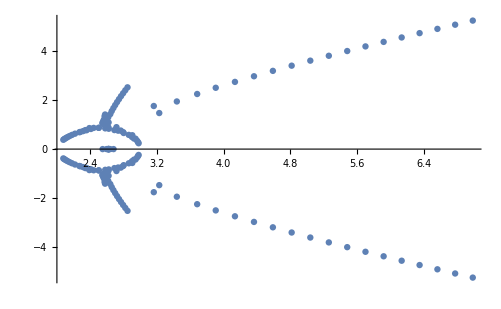

```mathematica
ListPlot[Map[{Re[#],Im[#]}&,Flatten[d3]], PlotRange->All]
```

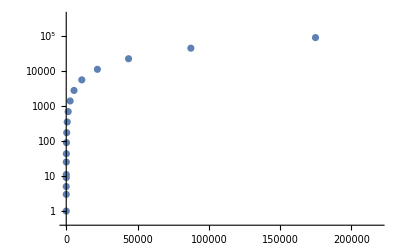

```mathematica
ListLogPlot[Monitor[Table[
With[{g=JacobsThalGraph[k]},
With[
{h=Rule2[g,1<->4,5<->2]},
{ChromaticPolynomial[g,4]/24,ChromaticPolynomial[h,4]/24}
]
]
,{k,1,20}],k]]
```

```mathematica
VertexCount[JacobsThalGraph[6]]
```

10

```mathematica
VertexCount[WheelGraph[10]]
```

10

```mathematica
ChromaticPolynomial[JacobsThalGraph[1],4]
```

24

```mathematica
ChromaticPolynomial[WheelGraph[10],4]
```

2040

```mathematica
PaintGraph2First[ JacobsThalGraph[10]]
```

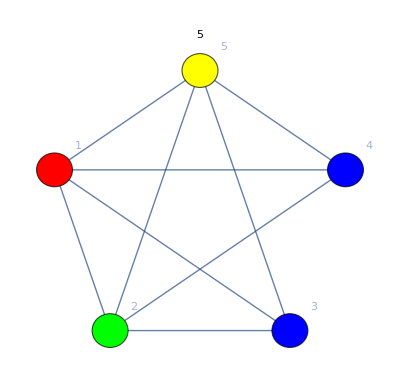
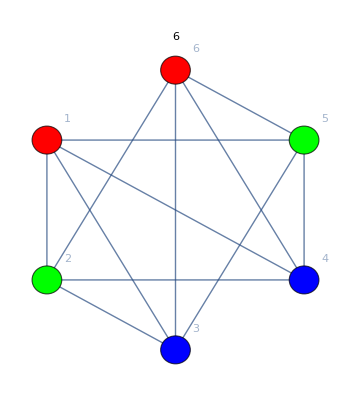
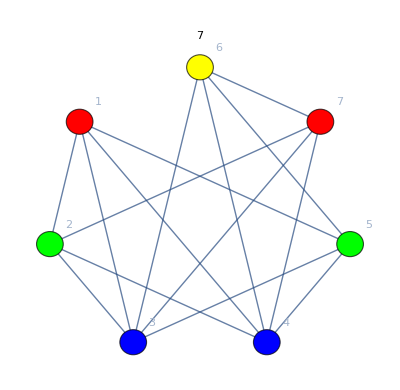
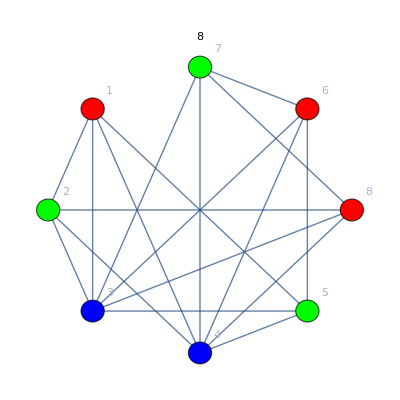
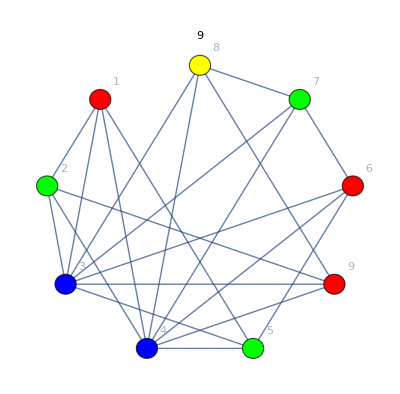
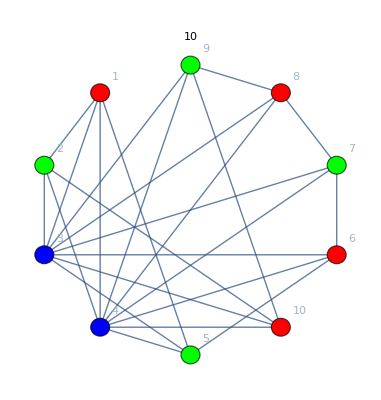
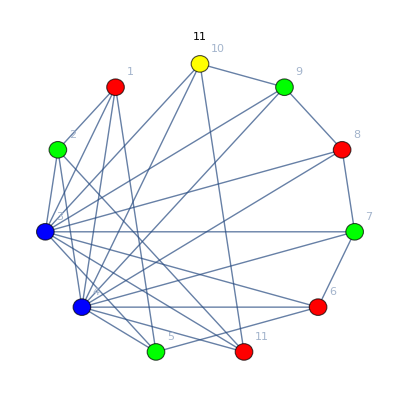
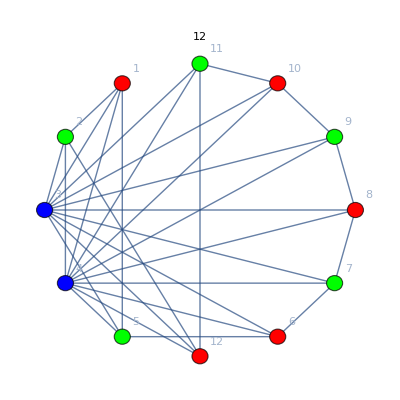

```mathematica
Table[With[{g=JacobsThalGraph[k]},PaintGraph2First[g,"x1==1&&x2==2&&x3==3",VertexLabels->"Name",GraphLayout->"CircularEmbedding",PlotLabel->VertexCount[g]]],{k,1,15}]
```